# Visibility definitions

From https://www.pnas.org/doi/10.1073/pnas.0709247105 and https://arxiv.org/pdf/1002.4526.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/blmayer/repos/thesis

## Natural Visibility

More formally, we can establish the following visibility criteria : two arbitrary data values (t_a, y_a) and (t_b, y_b) will have visibility, and consequently will become two connected nodes of the associated graph, if any other data (t_c, y_c) placed between them fulfills:
-Graphics-

```mathematica
visibleQ[a_Integer, b_Integer, ts_List]:=Catch[
	Do[
		If[Not[ts[[x,2]] < ts[[b,2]] + (ts[[a,2]] − ts[[b,2]])(ts[[b,1]]−ts[[x,1]])/(ts[[b,1]]−ts[[a,1]])],Throw[False]],
		{x,a+1,b-1}
	];
	Throw[True]
]
```

```mathematica
naturalVisibility[series_]:=Block[{visibles},
	visibles={};
	SetSharedVariable[visibles];
	ParallelDo[
		Do[
			If[visibleQ[i,j,series],AppendTo[visibles,series[[i,1]]->series[[j,1]]]],
			{j,i+1,Length@series}
		],
		{i,1,Length@series-1}
	];
	Return[visibles]
]
```

### Testing

```mathematica
ts={{1,1},{7,2},{10,4},{13,2},{19,2},{23,2},{28,6},{31,2},{32,6},{44,6},{49,3},{68,6},{70,8},{79,2},{82,4},{86,4},{91,4},{94,4}};
```

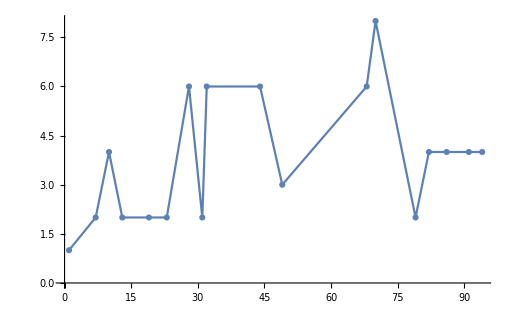

```mathematica
ListLinePlot[ts,PlotMarkers->Automatic]
```

```mathematica
naturalVisibility[ts]
```

{1→7,23→28,1→10,28→31,7→10,28→32,10→13,28→70,10→19,31→32,10→23,32→44,10→28,32→70,13→19,13→28,44→49,19→23,44→68,19→28,44→70,49→68,79→82,49→70,82→86,68→70,86→91,70→79,91→94,70→82,70→86,70→91,70→94}

```mathematica
visibleQ[1,3,ts]
```

True

```mathematica
visibleQ[1,4,ts]
```

False

```mathematica
visibleQ[3,6,ts]
```

True

```mathematica
visibleQ[3,7,ts]
```

True

```mathematica
visibleQ[3,8,ts]
```

False

```mathematica
visibleQ[7,9,ts]
```

True

```mathematica
visibleQ[7,10,ts]
```

False

```mathematica
visibleQ[7,13,ts]
```

True

## Horizontal Visibility

x_i,x_j>x_n for all n such that  i<n<j.

```mathematica
horizontalQ[a_Integer, b_Integer, ts_List]:=Catch[
	Do[
		If[Not[ts[[x,2]] < ts[[a,2]] && ts[[x,2]] < ts[[b,2]]],Throw[False]],
		{x,a+1,b-1}
	];
	Throw[True]
]
```

```mathematica
horizontalVisibility[series_]:=Block[{visibles},
	visibles={};
	SetSharedVariable[visibles];
	ParallelDo[
		Do[
			If[horizontalQ[i,j,series],AppendTo[visibles,series[[i,1]]->series[[j,1]]]],
			{j,i+1,Length@series}
		],
		{i,1,Length@series-1}
	];
	Return[visibles]
]
```

### Testing

```mathematica
ts={{1,1},{7,2},{10,4},{13,2},{19,2},{23,2},{28,6},{31,2},{32,6},{44,6},{49,3},{68,6},{70,8},{79,2},{82,4},{86,4},{91,4},{94,4}};
```

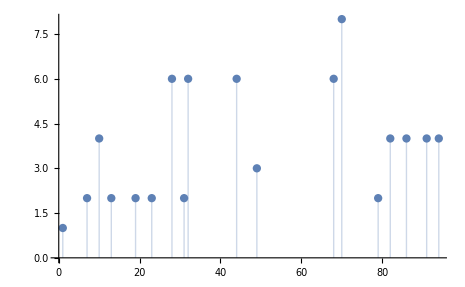

```mathematica
ListPlot[ts,Filling->Bottom]
```

```mathematica
horizontalVisibility[ts]
```

{1→7,23→28,7→10,28→31,10→13,28→32,10→28,31→32,13→19,32→44,19→23,44→49,79→82,44→68,82→86,49→68,86→91,68→70,91→94,70→79,70→82}

```mathematica
SubsetQ[naturalVisibility[ts],horizontalVisibility[ts]]
```

True

```mathematica
horizontalQ[1,2,ts]
```

True

```mathematica
horizontalQ[1,3,ts]
```

False

```mathematica
horizontalQ[3,4,ts]
```

True

```mathematica
horizontalQ[3,5,ts]
```

False

```mathematica
horizontalQ[3,7,ts]
```

True

```mathematica
horizontalQ[3,9,ts]
```

False

```mathematica
horizontalQ[9,10,ts]
```

True

```mathematica
horizontalQ[9,11,ts]
```

False

```mathematica
horizontalQ[9,12,ts]
```

False

```mathematica
horizontalQ[10,11,ts]
```

True

```mathematica
horizontalQ[10,12,ts]
```

True

```mathematica
horizontalQ[10,13,ts]
```

False

```mathematica
plotModel[count_, len_]:=Block[
{countrel,nlm,x,C,γ},
countrel=Table[{x,Lookup[count,x]/len}, {x,Keys[count]}];
nlm=NonlinearModelFit[countrel,C x^-γ,{C,γ},x];
{
{#1,Differences[#2][[1]]/2}&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]],
Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],
Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
}
]
```

```mathematica
plotLinearModel[count_, len_]:=Block[
{countrel,nlm,x,points},
countrel=Table[{x,Lookup[count,x]/len}, {x,Keys[count]}];
points=Log@countrel;
lm=LinearModelFit[points,x,x];
Show[
ListPlot[points,PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
Plot[lm[x],{x,0,8.1},PlotRange->{{0,8.1},All},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large,AspectRatio->0.8
]
]
```

```mathematica
Save[NotebookDirectory[]<>"visibility.wl",{visibleQ, horizontalQ,naturalVisibility,horizontalVisibility,plotModel,plotLinearModel}];
```